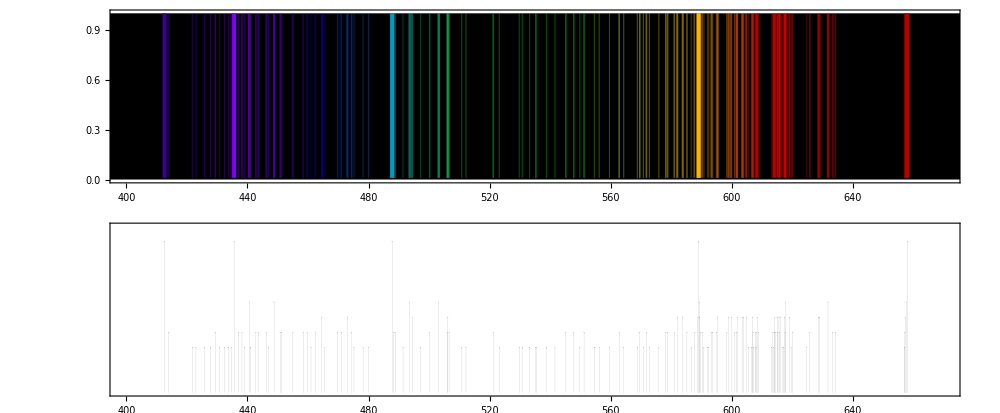

```mathematica
SetDirectory[NotebookDirectory[]];
<<data.m;

(*
Обозначения интенсивностей спектральных линий: 
сверхсильная — 1;
сильная — 0.6;
средняя — 0.5;
слабая — 0.4;
сверхслабая — 0.3
*)


ChromaticityPlot;
newVisibleSpectrum=With[{colors={Image`ColorOperationsDump`$wavelengths,XYZColor@@@Image`ColorOperationsDump`tris}ᵀ},Blend[colors,#]&];

spectrum[list_List]:=Graphics[{Thickness[0.005*#[[2]]],Opacity[#[[2]]],newVisibleSpectrum[#[[1]]],Line[{{#[[1]],0.01},{#1[[1]],1}}]}&/@list,PlotRange->{{400,670},{0,1}},PlotRangePadding->None,ImagePadding->All,AspectRatio->1/5,ImageSize->Large,Axes->None,FrameTicksStyle->Directive[13],Frame->{True,False,False,False},Prolog->Rectangle[{0,0},{1000,1}]]

imgH2=spectrum[H2];
histimg = ListPlot[H2,PlotRange->{{400,670},{0,1.1}},
PlotStyle->{AbsolutePointSize[0],Gray},
PlotRangePadding->None,ImagePadding->All,AspectRatio->1/5,ImageSize->Large,Axes->None,Frame->{True,False,False,False},
FrameTicks->{Automatic,None},Filling->Axis,
FrameTicksStyle-> Directive[FontSize->12],
FillingStyle->Directive[Thickness -> .00,Gray] ];
spectrumimg  = GraphicsColumn[{imgH2,histimg},ImageSize->1000]
```